# Infra Bundles

We start with a finite graph and a projection of its vertices. Equal fibers, lift existence, unique lifting and bundle structure are separate properties. Sections and complete connections add choices to this data.

## Topological language and finite readings

The finite object is a graph with a vertex projection. The following dictionary distinguishes its exact conditions from the additional structures of continuous topology.

| Topological notion | Finite infra reading | Qualification
       | Projection from total space to base | InfraFiberedGraph with InfraTotalSpace, InfraBaseSpace and InfraProjection | The base graph is reconstructed from projected edges; no topology is part of the inert object.
       | Serre or Hurewicz fibration | InfraFibrationQ asks for a lift of every base edge from every starting vertex | This is weak edge-lift existence, not a homotopy-lifting axiom.
       | Covering space | InfraCoveringQ gives edgeless fibers and a bijection on vertex neighbourhoods | The graph-covering condition has the usual covering interpretation under graph realization. Sheet counts can differ across base components.
       | Fiber bundle | InfraFiberBundleQ gives a common fiber graph and adjacency-preserving transverse matchings | This is an edgewise Cartesian graph bundle. Realizing its edges alone does not supply topological product charts or filled squares.
       | Section | InfraSection chooses a right inverse on a base domain | InfraContinuousSectionQ asks for adjacency preservation on that domain.
       | Connection and parallel transport | InfraConnection selects complete fiber matchings; transport composes them | This is finite bijective transport. Preserving a fiber graph is an additional condition.
       | Infra-only transverse local conditions | InfraAtMostOneEdgeLiftQ and InfraFibrationQ read injectivity and surjectivity on transverse neighbours | Vertical neighbours are excluded; the conditions do not assert local injectivity or surjectivity in a chosen topology.
       | Infra-only multiplicity and equitable partition | InfraEdgeLiftMultiplicity counts transverse neighbours, including zeros | Constancy within each fiber is transverse equitability; full equitability also needs constant vertical degree.

For the continuous definitions, see Hatcher, Algebraic Topology, Sections 1.3 and 4.2. The finite definitions and their implications are developed below.

## Setup

```mathematica
Needs[ "WolframInstitute`InfraGeometry`" ]
```

## Total space, projection and fibers

A fibered graph consists of a finite simple undirected unweighted untagged graph E and a map π on its vertices. The base graph B has vertex set π(V(E)). Distinct base vertices are adjacent exactly when some total edge joins their preimages. The fiber F_p is the induced graph on π^-1(p). A total edge is vertical when both endpoints project to the same vertex, and transverse otherwise.

The object carries no drawing, connection or lifting axiom. The base includes isolated projection values, and projection collapses vertical edges. The empty graph with empty projection is allowed.

| Object or reading | Interface
       | Inert total graph and projection | InfraFiberedGraph[total, projection]
       | Total graph | InfraTotalSpace[fib]
       | Reconstructed base graph | InfraBaseSpace[fib]
       | Projection association | InfraProjection[fib]
       | One induced fiber; all induced fibers | InfraFiber[fib,p]; InfraFibers[fib]
       | Supported fibered graph | InfraFiberedGraphQ[fib]

The projection may be an association or a function. Association keys are literal total vertices; lists are allowed as individual labels.

A cycle wraps twice around its reconstructed square base. The marked vertices form one fiber.

```mathematica
SeedRandom[ 7 ];
With[ { fib = InfraFiberedGraph[ CycleGraph[ 8 ], vertex |-> Mod[ vertex, 4, 1 ] ] },
  GraphicsRow[ { InfraFiberedGraphHighlight[ fib, { InfraFiber[ fib, 1 ] } ],
    InfraTotalSpace[ fib ], InfraBaseSpace[ fib ] } ] ]
```

-Graphics-

## Local multiplicity and structural properties

For a total vertex x over p and a neighbour q of p, define the edge-lift multiplicity

m(x,q)=|{y∈V(F_q):{x,y}∈E(E)}|.

The multiplicity reader returns an association from each total vertex to an association of adjacent base vertices and their counts. Zero counts record missing lifts. Vertical neighbours are excluded. A total vertex over an isolated base vertex has an empty inner association.

| Condition | Finite meaning | Reader
       | Weak graph continuity | Every total edge projects to a base edge or a vertex; automatic for the reconstructed base | InfraFiberedGraphQ
       | Equal fiber sizes | Every fiber has the same cardinality, including across base components | InfraEqualFiberSizesQ
       | Isomorphic fibers | All induced fiber graphs are mutually isomorphic | InfraIsomorphicFibersQ
       | Local surjectivity on transverse neighbours | Every multiplicity is positive; the project's weak fibration condition | InfraFibrationQ
       | Local injectivity on transverse neighbours | Every multiplicity is at most one | InfraAtMostOneEdgeLiftQ
       | Unique edge lifting | Every multiplicity is one | InfraUniqueEdgeLiftingQ
       | Graph bundle | Isomorphic fibers and unique lifts whose matchings preserve vertical adjacency | InfraFiberBundleQ
       | Graph covering | Unique edge lifting and no vertical edges | InfraCoveringQ
       | Transverse equitable multiplicity | For each base vertex, the inner multiplicity association is constant throughout its fiber | Read with InfraEdgeLiftMultiplicity

The last row is a condition one can read from the existing measurement; it adds no predicate. A full equitable partition also requires constant vertical degree within each fiber. The local injectivity and surjectivity rows concern transverse neighbours only. They are exact finite conditions, without a chosen topology on the vertices.

Here one transverse edge reconstructs a base edge, but two total vertices have no lift of it.

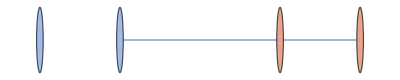
{-Graphics-,<|1→<|q→1|>,2→<|q→0|>,3→<|p→1|>,4→<|p→0|>|>}

```mathematica
SeedRandom[ 7 ];
With[ { fib = InfraFiberedGraph[ Graph[ Range[ 4 ], { UndirectedEdge[ 1, 3 ] } ],
    <| 1 -> "p", 2 -> "p", 3 -> "q", 4 -> "q" |> ] },
  { InfraFiberedGraphHighlight[ fib ], InfraEdgeLiftMultiplicity[ fib ] } ]
```

Lift existence and at-most-one lifting together give unique lifting. Over a base edge, unique lifting gives a perfect matching: every vertex on either side has degree one. Consequently, fiber sizes agree within each connected base component. They need not agree between components.

Isomorphic fibers imply equal sizes, but impose no transverse-edge condition. A covering over a connected base is a bundle with a discrete fiber. A covering on a disconnected base may have different sheet counts and then lacks one common fiber.

These predicates treat the empty fibered graph vacuously. A nonempty list of objects is tested by conjunction; an empty list gives False. Malformed projections, unsupported graph domains and unknown construction heads remain unevaluated. Supported Experimental models have explicit predicate methods that materialize once; converting them to a literal object by hand is optional.

## Generate a prescribed class

The generator retains every vertex and edge of the supplied base in the reconstructed base. Its default property list requests general fibered graphs. Properties are a flat conjunction of the conditions named in the symbol reference.

| Count specification | Meaning
       | n | An upper bound; the minimum is one for fiber vertices and zero for vertical edges
       | {n} | Exactly n
       | {lo,hi} | A discrete uniform integer from lo through hi
       | Automatic, for horizontal edges | A count feasible for the requested properties
       | All, for horizontal edges | The complete join, when compatible with the requested properties

Scalar edge caps intersect the property-feasible interval. Exact counts and ranges must fit every permitted fiber size; they are never clipped. Count draws are uniform on their admissible interval; graph samples are not asserted uniform. See RandomInfraFiberedGraphpaclet:WolframInstitute/InfraGeometry/ref/RandomInfraFiberedGraphWolframInstitute/InfraGeometry Package Symbol for the joint size and edge-count constraints.

The first graph has independent fiber sizes. The second has isomorphic fibers and lift existence. The third is a graph bundle.

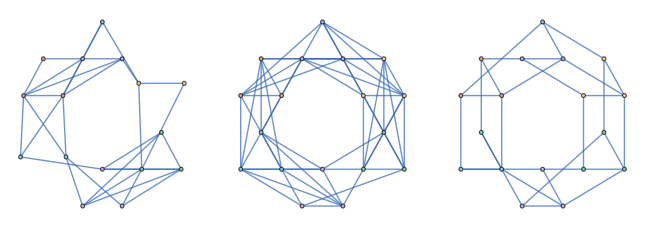

```mathematica
SeedRandom[ 7 ];
With[ { base = CycleGraph[ 6 ] },
  GraphicsRow[ InfraFiberedGraphHighlight /@ {
    RandomInfraFiberedGraph[ base, "VerticalVertexCount" -> { 2, 4 }, "VerticalEdgeCount" -> 2, RandomSeeding -> 7 ],
    RandomInfraFiberedGraph[ base, Properties -> { "IsomorphicFibers", "Fibration" },
      "VerticalVertexCount" -> { 3 }, "VerticalEdgeCount" -> { 2 }, RandomSeeding -> 7 ],
    RandomInfraFiberedGraph[ base, Properties -> { "FiberBundle" },
      "VerticalVertexCount" -> { 3 }, "VerticalEdgeCount" -> { 2 }, RandomSeeding -> 7 ] } ] ]
```

## Sections and extensions

A section on a domain chooses one total vertex over each base vertex in that domain. It is continuous when every base edge within the domain maps to a total edge. A partial section fixes values to be preserved by an extension.

The default section class is set-theoretic on every overload. A domain list restricts the target; an inert section supplies prescribed values and requests extension over the whole base. The continuous property is requested explicitly.

Complete joins let a partial section extend continuously in every choice of the remaining fibers.

```mathematica
SeedRandom[ 7 ];
With[ { fib = RandomInfraFiberedGraph[ CycleGraph[ 6 ],
    "VerticalVertexCount" -> { 3 }, "HorizontalEdgeCount" -> All, RandomSeeding -> 7 ] },
  { partial = RandomInfraSection[ fib, { 1, 3 }, RandomSeeding -> 7 ] },
  { section = RandomInfraSection[ fib, partial, Properties -> { "Continuous" }, RandomSeeding -> 7 ] },
  InfraFiberedGraphHighlight[ fib, { partial, section } ] ]
```

-Graphics-

Section and connection samplers return one object by default. An integer result count requests exactly that many distinct objects, a capped count requests at most that many, and All enumerates the class. An exact shortage gives an empty result list. These result counts are distinct from the vertex and edge count specifications above.

The external random seed controls bounded random searches. Identity ordering and default complete enumeration are deterministic. A pruning callback restricts the searched class, so a shortage under that callback need not mean mathematical nonexistence.

## Complete connections and horizontal lifts

A complete connection selects a perfect matching between the whole fibers over every base edge, using transverse total edges. It selects no vertical edges. A matching transports fiber vertices bijectively, but need not preserve vertical adjacency.

Lift existence alone does not supply a complete connection. In this example every total vertex has a transverse neighbour, but the first two vertices of one fiber share only one possible target. No perfect matching can use distinct targets for both.

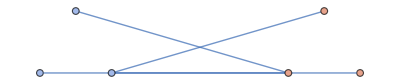

```mathematica
SeedRandom[ 7 ];
With[ { fib = InfraFiberedGraph[ Graph[ Range[ 6 ],
    UndirectedEdge @@@ { { 1, 4 }, { 2, 4 }, { 3, 5 }, { 3, 6 } } ],
    <| 1 -> "p", 2 -> "p", 3 -> "p", 4 -> "q", 5 -> "q", 6 -> "q" |> ] },
  { InfraFiberedGraphHighlight[ fib ], RandomInfraConnection[ fib, All ] } ]
```

A complete connection lifts each base walk uniquely after a starting total vertex is chosen. The result is an ordered vertex list, including repeated visits. Parallel transport records its endpoint for every start in the initial fiber.

The selected connection below determines the highlighted lift.

```mathematica
SeedRandom[ 7 ];
With[ { fib = RandomInfraFiberedGraph[ CycleGraph[ 6 ],
    "VerticalVertexCount" -> { 3 }, "HorizontalEdgeCount" -> All, RandomSeeding -> 7 ] },
  { connection = RandomInfraConnection[ fib, RandomSeeding -> 7 ] },
  { start = First @ VertexList @ InfraFiber[ fib, 1 ] },
  { lift = InfraHorizontalLift[ fib, connection, start, { 1, 2, 3, 4, 5, 6, 1 } ] },
  InfraFiberedGraphHighlight[ fib, { connection, InfraWalk[ lift ] } ] ]
```

-Graphics-

If all fibers are mutually isomorphic and the selected matchings preserve their adjacency, the vertical edges and selected transverse edges form a graph bundle. A raw fibered graph may contain additional transverse edges, so this statement concerns the selected subgraph.

## Twisting and holonomy

The holonomy of a closed base walk is the permutation produced by transport around it. Permutation positions refer to the vertex order of the starting fiber. A one-vertex loop gives the identity.

A graph bundle can be twisted. Both graphs below cover the same square with two points per fiber. The product has two horizontal leaves; the connected double cover exchanges the two points after one base circuit.

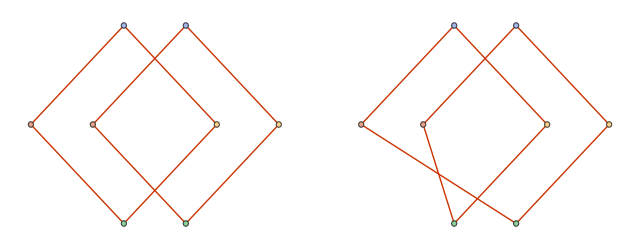

```mathematica
SeedRandom[ 7 ];
With[ { product = InfraFiberedGraph[ GraphProduct[ CycleGraph[ 4 ], Graph[ { 1, 2 }, { } ], "Cartesian" ], First ],
    twisted = InfraFiberedGraph[ CycleGraph[ 8 ], vertex |-> Mod[ vertex, 4, 1 ] ] },
  GraphicsRow[ Map[ fib |-> With[ { connection = InfraConnection[ EdgeList @ InfraTotalSpace[ fib ] ] },
    InfraFiberedGraphHighlight[ fib, connection ] ], { product, twisted } ] ] ]
```

The exchange is a transposition in the starting fiber.

```mathematica
SeedRandom[ 7 ];
With[ { fib = InfraFiberedGraph[ CycleGraph[ 8 ], vertex |-> Mod[ vertex, 4, 1 ] ] },
  { connection = InfraConnection[ EdgeList @ InfraTotalSpace[ fib ] ] },
  InfraHolonomy[ fib, connection, { 1, 2, 3, 4, 1 } ] ]
```

Cycles[{{1,2}}]

InfraTrivialMonodromyQpaclet:WolframInstitute/InfraGeometry/ref/InfraTrivialMonodromyQWolframInstitute/InfraGeometry Package Symbol tests trivial global monodromy: every closed base walk acts identically. This is equivalent to every horizontal leaf projecting injectively. Indeed, two vertices in one leaf over the same base vertex give a lifted closed walk between them. Conversely, a closed walk with distinct lift endpoints places two such vertices in one leaf.

Curvature needs a specified family of faces and their boundary loops. A graph alone supplies no such family. The global monodromy predicate therefore does not replace a face-based curvature definition.

## Three views of one object

Circular fibers, upright three-dimensional fibers and the total graph's own layout display the same finite object. Highlights preserve their meaning in every view.

```mathematica
SeedRandom[ 7 ];
With[ { fib = RandomInfraFiberedGraph[ CycleGraph[ 6 ],
    "VerticalVertexCount" -> { 3 }, "HorizontalEdgeCount" -> All, RandomSeeding -> 7 ] },
  { section = RandomInfraSection[ fib, Properties -> { "Continuous" }, RandomSeeding -> 7 ],
    connection = RandomInfraConnection[ fib, RandomSeeding -> 7 ] },
  GraphicsRow[ Map[ method |-> InfraFiberedGraphHighlight[ fib, { section, connection }, Method -> method ],
    { "CircularFiber", "3DFiber", "HighlightFiber" } ] ] ]
```

-Graphics-

The viewer fixes the structure and layout when created. Hovering a base vertex inspects its fiber; hovering a base edge inspects supplied section and connection edges above it. Live hovering requires the notebook front end.

```mathematica
SeedRandom[ 7 ];
With[ { fib = RandomInfraFiberedGraph[ CycleGraph[ 6 ],
    "VerticalVertexCount" -> { 2 }, "HorizontalEdgeCount" -> All, RandomSeeding -> 7 ] },
  { connection = RandomInfraConnection[ fib, RandomSeeding -> 7 ] },
  InfraFiberedGraphViewer[ fib, connection ] ]
```

## Relation to bundle terminology

The graph-bundle condition is edgewise: the preimage of each base edge is its Cartesian product with the common fiber, respecting the projection. This is the Cartesian graph-bundle convention in the graph literature; it permits global twisting. See Algorithm for recognizing Cartesian graph bundles.

A topological fiber bundle instead requires product charts over open neighbourhoods. Topological covering spaces have unique path lifting; a covering over a disconnected base can have different sheet counts. These are separate statements about topological spaces, as in Hatcher, Algebraic Topology, Sections 1.3 and 4.2. The finite predicates here assert neither Serre nor Hurewicz homotopy lifting.

The broad object and separate predicates follow the April 2026 Meeting 1 notes of Pavel Hajek, Ioana Milea and Stephen Wolfram, unpublished. Ioana Milea's one-page Fibered Graph Gauge Theory Basics motivates fiber automorphisms and permutation holonomy. A matching of sets becomes a fiber-graph isomorphism only when it also preserves vertical adjacency.

## Compatibility

| Earlier spelling | Canonical spelling
       | InfraFibration | InfraFiberedGraph
       | InfraTotalGraph | InfraTotalSpace
       | InfraBaseGraph | InfraBaseSpace
       | InfraFibrationAssociation | InfraProjection

Existing literal objects remain accepted by the readers and operations. The earlier random generator retains its distinct option grammar as Experimental compatibility functionality. Particular geometric models and scale or completion questions are treated in Experimental Infra Bundlespaclet:WolframInstitute/InfraGeometry/tutorial/ExperimentalInfraBundles.

Related Guides

InfraFiberBundlespaclet:WolframInstitute/InfraGeometry/guide/InfraFiberBundles

Related Tech Notes

ExperimentalInfraBundlespaclet:WolframInstitute/InfraGeometry/tutorial/ExperimentalInfraBundles

## Metadata

### Categorization

Tutorial

WolframInstitute/InfraGeometry

WolframInstitute`InfraGeometry`

WolframInstitute/InfraGeometry/tutorial/InfraBundles

### Keywords

fibered graph

graph bundle

covering

edge lifting

multiplicity

section

connection

holonomy